# CCBH-Power Law + Peak: ParameterDependenceTest

Davi  C. Rodrigues (this code). July-September, 2023.

```mathematica
ResourceFunction["DarkMode"][]
```

CCBH = Cosmologically coupled black hole (general case)
DEBH = Dark energy coupled Black Hole (implies k = - 3w)
GBH = Growing BH, k is arbitrary and without direct dark energy impact.
m1 = primary (larger) mass of the BBH or NSBH pair.

Naming conventions:
All defined variables/functions start with lower case letter.
“I” at the end of a function name: interpolated version. 
“Raw”: a function without options. It is useful to store results. The version with options is based on the raw version.

## Starting...

```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{"codes", "Directories.wl"}]];

(*
  Calling wl files
  ***************** 
*)

getCode["Constants.wl"];
baseSimPoints = 5 10^5; (*The base number of points to be simmulated for each dimension, commonly 10^5-10^7, depends on the purpose.*)

getCode["PowerLawPlusPeakDefinition.wl"];
getCode["Cosmology.wl"];

Print["End of running wl files."];

(*
  GENERAL PURPOSE FUNCTIONS
  **************************
*)

sigmaProb::usage = "sigmaProb[probability] yields the number of σ's for a given probability.";
sigmaProb[prob_] := Block[{sigma}, 
  sigma /. FindRoot[NProbability[RealAbs[x] > sigma , x\[Distributed]NormalDistribution[]] == prob, {sigma, 0, 10}]
];

Clear[probSigma];
probSigma[n_] := probSigma[n] = NProbability[RealAbs[x] > n, x\[Distributed]NormalDistribution[]];
```

Starting Constants.wl:

Starting PowerLawPlusPeakDefinition.wl:

Use plpp`pi[m, options] for the power-law-plus-peak PDF and plpp`𝒟[options] for the distribution. Use optionsPlpp to see the options.

Starting Cosmology.wl:

tableZformation loaded.

End of running wl files.

## Testing PLPP parameter dependence (using 3 10^5)

here I have to select randomly different PLPP values and find the probability with reference values.

```mathematica
(*The quantiles for GWTC-3 PLPP parameters, 5%, 16%, Median, 84%, 95%. Provided by Sumit Kumar.*)

(*
alpha = Around[#3, {#1 - #3, #5-#3 }] & @@ Evaluate@ReleaseHold[Hold[2.91368096 3.10533638 3.40401232 3.73461844 3.98690423] /. Times -> List];
beta =  Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[-0.24646612  0.23829546  1.07679192  2.04662647  2.83787879] /. Times -> List ] ;
mmax = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[77.49731724 79.92731197 86.85433456 94.93299396 98.2530281] /. Times -> List ];
mmin = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[3.55443173 4.21290074 5.08383396 5.68043848 5.95357982] /. Times -> List ];
lam = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[0.01308824 0.02074258 0.03868563 0.06805879 0.09687909] /. Times -> List ];
mpp = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[29.93629207 31.68191701 33.72549972 35.13203767 35.98450818] /. Times -> List ];
sigpp = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[1.45384514 2.07879345 3.55853002 6.07252803 8.14412684] /. Times -> List ];
deltam = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[1.60127061 2.97112556 4.82841 6.8000636  8.15460135] /. Times -> List ];
*)

(*
  minA[around_] := around /. Around[x_, y_] :>  x - y[[1]];
  maxA[around_] := around /. Around[x_, y_] :>  x + y[[2]];
  randomPP[parameter_] := RandomVariate[UniformDistribution[{minA[parameter], maxA[parameter]}]];
*)

assoSamplesPLPPraw = Import[FileNameJoin[{pathIn, "all_samples_PLPP_GWTC3.h5"}], "Data"]; (*Data imported as association, asso for short.*)
assoSamplesPLPP = KeyMap[StringDelete[#, {"/", "_"}] & , assoSamplesPLPPraw]; (*Removes inconvenient strings from the key names.*) 

alpha = assoSamplesPLPP["alpha"];
beta = assoSamplesPLPP["beta"];
mmax = assoSamplesPLPP["mmax"];
mmin = assoSamplesPLPP["mmin"];
lam = assoSamplesPLPP["lam"];
mpp = assoSamplesPLPP["mpp"];
sigpp = assoSamplesPLPP["sigpp"];
deltam = assoSamplesPLPP["deltam"];

lengthSample = Length @ alpha;
```

Modified version of the MassFactorCorrection.wl code, to allow for parameter variation: no memory.

```mathematica
ClearAll[
  massFactorDelay, 
  dataMassFactor,
  dataDelayTime,
  minDelayTime, 
  maxDelayTime
];

Echo[baseSimPoints, "Base number of simmulated points per dimension (baseSimPoints): "];

listDelayTime = Range[tdmin0/10, tdmax0, 0.015]; (* delayTime values to be computed. tdmin lower than tdmin0 will be considered*)
listzObs = Range[0.0, 1.0, 0.01];
listw = Range[-1.5, -0.5, 0.1]; 

minDelayTime = First[listDelayTime]; (*min delay time to be computed, it can be lower than tdmin0*)
maxDelayTime[zObs_, tdmax_?NumberQ, zMax_?NumberQ, w_] :=  Min[
  tdmax,
  timeZ[zObs, zMax, w]
]; 

massFactor[zObs_,zFormation_, k_] = ((1 + zFormation)/(1 + zObs))^k; (*(a/a_i)^k. This is the factor that corrects the mass*)

SetAttributes[massFactorDelay, Listable];
massFactorDelay[zObs_, delayTime_, k_, zMax_, w_] =  massFactor[zObs, zFormationI[zObs, delayTime, zMax, w], k];

randomLogDelayTime[zObs_, tdmin_, tdmax_, zMax_, w_, realizations_] := 
 RandomReal[{Log10[tdmin], Log10 @ maxDelayTime[zObs, tdmax, zMax, w]}, realizations]; (*log-flat distribution.*)

dataDelayTime[zObs_, tdmin_, tdmax_, zMax_, w_] := 
 10^randomLogDelayTime[zObs, tdmin, tdmax, zMax, w,  proportionalBaseSimPoints[tdmin, tdmax]]; 

dataMassFactor[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := dataMassFactor[zObs, tdmin, tdmax, k, zMax, w] =
 massFactorDelay[zObs, dataDelayTime[zObs, tdmin, tdmax, zMax, w], k, zMax, w];
 
(*
  FORMATION MASS
  ***********
*)

(* ::Section:: *)
(* Formation Mass *)

Clear[dataM1FormationRaw, dataM1Formation, dataM1Merger];

Clear[𝒟plp];
tabRandom = {};
𝒟plp := (
  random = RandomInteger[lengthSample];
  AppendTo[tabRandom, random];
  plpp`dist[
    plpp`a -> alpha[[random]],
    plpp`mMin -> mmin[[random]],
    plpp`dm -> deltam[[random]],
    plpp`mMax -> mmax[[random]],
    plpp`mu -> mpp[[random]],
    plpp`s -> sigpp[[random]],
    plpp`l -> lam[[random]],
    plpp`betaQ -> beta[[random]]
  ]
); (*plpp`𝒟 is defined in PowerLawPlusPeakDefinition.wl.*)

dataM1Merger := RandomVariate[𝒟plp, baseSimPoints];  (*2 baseSimPoints is not necessary here*)

dataM1FormationRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_]:= Block[
  {length, dataM1MergerSameLength},
  length = Length @ dataMassFactor[zObs, tdmin, tdmax, k, zMax, w];
  dataM1MergerSameLength = Take[dataM1Merger, length];
  1/dataMassFactor[zObs, tdmin, tdmax, 1, zMax, w]^k dataM1MergerSameLength 
];

dataM1Formation[zObs_, opts:OptionsPattern[optionstkw]] := dataM1FormationRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];

𝒟M1FormationEmpRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 
 EmpiricalDistribution[
   dataM1FormationRaw[zObs, tdmin, tdmax, k, zMax, w]
 ];

𝒟M1FormationEmp[zObs_, opts:OptionsPattern[optionstkw]] := 𝒟M1FormationEmpRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];

probabilityMminApprox[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M1FormationEmp[0.4, opts], mMin]^72;
probabilityMminApproxF[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M1FormationEmp[0.4, opts], mMin]^250; (*forecast*)
```

Base number of simmulated points per dimension (baseSimPoints):   500000

```mathematica
isComputeTension3 = False; (*Takes 4 hours for 10^3 probabilities, saved with baseSimPoints = 5 10^5. FOR THE OLD CODE, CURRENT ONE IS ABOUT 1/5 THE TIME*) 

If[isComputeTension3, 
  Echo["Computing the tension..."];
  listProbSamplePLPP3 = Monitor[Table[sigmaProb[probabilityMminApprox[2]], {i, 1000}], i]; // EchoTiming;
  dumpsave["listProbSamplePLPP3.mx", listProbSamplePLPP3];
  dumpsave["tabRandomPLPP3.mx", tabRandom],
  (*else*)
  getAux["listProbSamplePLPP3.mx"];
  Echo["listProbSamplePLPP3.mx loaded."];
];
```

listProbSamplePLPP3.mx loaded.

```mathematica
isComputeTensionk1Current = False;  (*About 40 minutes*)

If[isComputeTensionk1Current, 
  Echo["Computing the tension..."];
  tabRandom = {};
  listProbSamplePLPP1 = Monitor[Table[{#, sigmaProb[#]}&[probabilityMminApprox[2, k -> 1]], {i, 1000}], i]; // EchoTiming;
  dumpsave["listProbSamplePLPP1.mx", listProbSamplePLPP1];
  dumpsave["tabRandomPLPP1.mx", tabRandom],
  (*else*)
  getAux["listProbSamplePLPP1.mx"];
  Echo["listProbSamplePLPP1.mx loaded."];
]; (*NIntegrate convergence warnings may appear, but they are related to small NIntegrate errors.*)
```

Computing the tension...

2908.79

```mathematica
isComputeTensionk3F = False; 

If[isComputeTensionk3F, 
  Echo["Computing the tension..."];
  tabRandom = {};
  listProbSamplePLPP3F = Monitor[Table[{#, sigmaProb[#]}&[probabilityMminApproxF[2, k -> 3]], {i, 1000}], i]; // EchoTiming;
  dumpsave["listProbSamplePLPP3F.mx", listProbSamplePLPP3F];
  dumpsave["tabRandomPLPP3F.mx", tabRandom],
  (*else*)
  getAux["listProbSamplePLPP3F.mx"];
  Echo["listProbSamplePLPP3F.mx loaded."];
]; (*NIntegrate convergence warnings may appear, but they are related to small NIntegrate errors.*)
```

```mathematica
isComputeTensionk1F = False; 

If[isComputeTensionk1F, 
  Echo["Computing the tension..."];
  tabRandom = {};
  listProbSamplePLPP1F = Monitor[Table[{#, sigmaProb[#]}&[probabilityMminApproxF[2, k -> 1]], {i, 1000}], i]; // EchoTiming;
  dumpsave["listProbSamplePLPP1F.mx", listProbSamplePLPP1F];
  dumpsave["tabRandomPLPP1F.mx", tabRandom],
  (*else*)
  getAux["listProbSamplePLPP1F.mx"];
  Echo["listProbSamplePLPP1F.mx loaded."];
]; (*NIntegrate convergence warnings may appear, but they are related to small NIntegrate errors.*)
```

Computing the tension...

```mathematica
repeated = Select[Tally[tabRandom], Last[#] > 1 &][[All, 1]] // Length;
Echo[repeated/Length@tabRandom 100. "%", "Percentage of repeated realizations: "];
```

Percentage of repeated realizations:   3.6 %

```mathematica
color1i = RGBColor[0, 76/255, 153/255];
color1ii = RGBColor[51/255, 153/255, 255/255];
color2i = RGBColor[128/255, 0, 128/255];
color2ii = RGBColor[191/255, 85/255, 236/255];
color2iii = RGBColor[255/255, 140/255, 0];
color2iv = RGBColor[255/255, 179/255, 71/255];
color3i = RGBColor[0, 128/255, 128/255];
color3ii = RGBColor[0, 192/255, 192/255];
color3iii = RGBColor[139/255, 69/255, 19/255];
color3iv = RGBColor[210/255, 105/255, 30/255];


frameTicksHLarge = Table[{i, ToString@NumberForm[i, {2,1}]<>ToString@Style["σ", FontFamily-> "Times"], {0, 0.015}}, {i, 0, 10, 1}];
frameTicksHSmall = Table[{i, "", {0, 0.008}}, {i, 0, 10, .2}];
frameTicksHLargeD = Table[{i, None, {0.015,0}}, {i, 0, 10, 1}];
frameTicksHSmallD = Table[{i, None, {0.008,0}}, {i, 0, 10, .2}];
frameTicksH = Join[frameTicksHLarge, frameTicksHSmall];
frameTicksHD = Join[frameTicksHLargeD, frameTicksHSmallD];

plotHist[dataSigma_, color_] := Block[
  {
    median = Median@dataSigma,
    quantMin90 = Quantile[dataSigma, 0.05],
    quantMax90 = Quantile[dataSigma, 0.95],
    plot90,
    hist
  },
  plot90 = Plot[500, {x, quantMin90, quantMax90}, 
    Filling->Automatic, 
    FillingStyle->{Directive[Lighter@color, Opacity[0.2]]}, 
    Axes -> False, 
    Frame -> True , 
    Background->White, 
    PlotRangePadding->None
  ];
  
  hist = Histogram[
    dataSigma, 
    {0.1}, 
    Axes -> False, 
    Frame -> True , 
    Background->White, 
    ChartBaseStyle->EdgeForm[White], 
    ChartStyle->Directive[Opacity[0.8], color], 
    FrameStyle-> Directive[Black, FontSize -> 13]
  ];
  
  Show[{plot90, hist}, 
    PlotRange-> {{0,10}, {0,280}}, 
    FrameStyle-> Directive[Black, FontSize -> 13, FontFamily-> "Times"],
    FrameTicks-> {{Automatic, Automatic}, {frameTicksH, frameTicksHD}}
  ]
];
```

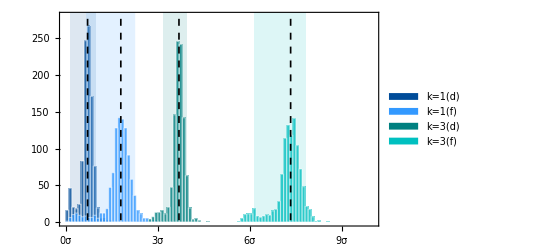

pathOut/histSamplePLPP1k3k.pdf

```mathematica
hist1 = plotHist[listProbSamplePLPP1[[All, 2]], color1i];
hist1F = plotHist[listProbSamplePLPP1F[[All, 2]], color1ii];
hist3 = plotHist[listProbSamplePLPP3, color3i];
hist3F = plotHist[listProbSamplePLPP3F[[All, 2]], color3ii];
median1 = Median @ listProbSamplePLPP1[[All, 2]];
median1F = Median @ listProbSamplePLPP1F[[All, 2]];
median3 = Median @ listProbSamplePLPP3;
median3F = Median @ listProbSamplePLPP3F[[All, 2]];

infL1 = InfiniteLine[{{median1, 0}, {median1, 1}}];
infL1F = InfiniteLine[{{median1F, 0}, {median1F, 1}}];
infL3 = InfiniteLine[{{median3, 0}, {median3, 1}}];
infL3F = InfiniteLine[{{median3F, 0}, {median3F, 1}}];

legend = SwatchLegend[
  {color1i, color1ii, color3i, color3ii}, 
  Style[#, FontFamily->"Times", 14]& /@ {"k=1(d)","k=1(f)","k=3(d)", "k=3(f)"}
];

histSamplePLPP1k3k = Show[
  {hist1, hist1F, hist3, hist3F}, 
  Epilog -> {
    Dashed, Black, Thickness[0.003], 
    infL1, infL1F, infL3, infL3F, 
    Inset[legend, Scaled[{0.88,0.75}]]
  }
]
(*exportOut["histSamplePLPP1k3k.pdf", histSamplePLPP1k3k]*)
```

## Adapting the direct method results plot

The plot below, named hist, was copied from `bh-cc-v16.nb`
The purpose of this section is simply to extract its data and plot it again using the above style.

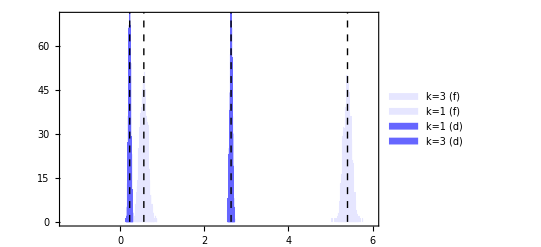
```mathematica
Clear[rectangles, computeBF, syntheticData, newHist, bins, frequencies, hist, lines, line];

hist  = -Graphics-;

lines = Cases[hist, _Line, Infinity] // Sort;
line[n_] := lines[[n]];

rectangles[1] = Select[Cases[hist,_Rectangle, {10}] , #[[1,1]] < 2 &] //. RoundingRadius -> "RoundingRadius";
rectangles[2] = Select[Cases[hist,_Rectangle, {7}] , #[[1,1]] < 5 &] //. RoundingRadius -> "RoundingRadius";
rectangles[3] = Select[Cases[hist,_Rectangle, {10}] , #[[1,1]] > 2 &] //. RoundingRadius -> "RoundingRadius";
rectangles[4] = Select[Cases[hist,_Rectangle, {7}] , #[[1,1]] > 5 &] //. RoundingRadius -> "RoundingRadius";

Clear[bins, frequencies, syntheticData];
transformation = Rectangle[{x1_,y1_},{x2_,y2_}, "RoundingRadius"->0] :> {Mean[{x1,x2}],y2};
computeBF[n_] := {bins[n], frequencies[n]} = rectangles[n] /. transformation // SortBy[#, First] & // Transpose;
syntheticData[n_] := Flatten[Table[RandomReal[{bins[n][[i]],bins[n][[i+1]]},frequencies[n][[i]]],{i,Length[frequencies[n]]-1}]];
newHist[n_] := Histogram[syntheticData[n],{bins[n]}];

computeBF /@ Range@4 ;

newHist /@ Range@4
```

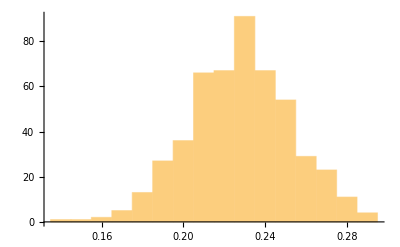
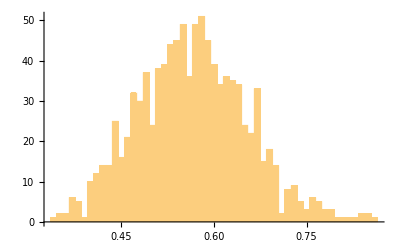
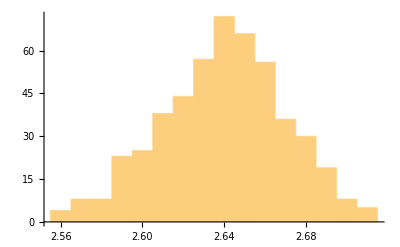
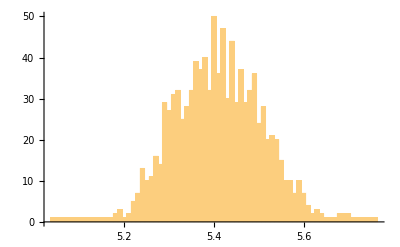

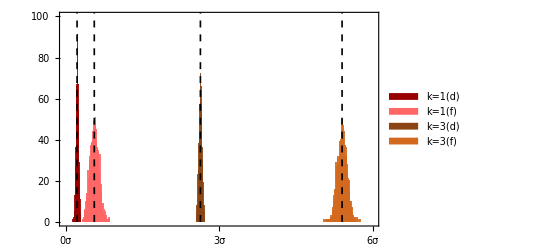

pathOut/histSampleDirect.pdf

```mathematica
color1i = RGBColor[0, 76/255, 153/255];
color1ii = RGBColor[51/255, 153/255, 255/255];
color1iii = RGBColor[153/255, 0, 0];
color1iv = RGBColor[255/255, 102/255, 102/255];
color2i = RGBColor[128/255, 0, 128/255];
color2ii = RGBColor[191/255, 85/255, 236/255];
color2iii = RGBColor[255/255, 140/255, 0];
color2iv = RGBColor[255/255, 179/255, 71/255];
color3i = RGBColor[0, 128/255, 128/255];
color3ii = RGBColor[0, 192/255, 192/255];
color3iii = RGBColor[139/255, 69/255, 19/255];
color3iv = RGBColor[210/255, 105/255, 30/255];

colorHist[1] = color1iii;
colorHist[2] = color1iv;
colorHist[3] = color3iii;
colorHist[4] = color3iv;


frameTicksHLarge = Table[{i, ToString@NumberForm[i, {2,1}]<>ToString@Style["σ", FontFamily-> "Times"], {0, 0.015}}, {i, 0, 10, 1}];
frameTicksHSmall = Table[{i, "", {0, 0.008}}, {i, 0, 10, .2}];
frameTicksHLargeD = Table[{i, None, {0.015,0}}, {i, 0, 10, 1}];
frameTicksHSmallD = Table[{i, None, {0.008,0}}, {i, 0, 10, .2}];
frameTicksH = Join[frameTicksHLarge, frameTicksHSmall];
frameTicksHD = Join[frameTicksHLargeD, frameTicksHSmallD];

plotNewHist[n_] := Block[{hist},
  hist = Histogram[
    syntheticData[n], 
    {bins[n]}, 
    Axes -> False, 
    Frame -> True , 
    Background->White, 
    ChartBaseStyle->EdgeForm[None], 
    ChartStyle->Directive[Opacity[0.9], colorHist[n]], 
    FrameStyle-> Directive[Black, FontSize -> 13]
  ];
  
  Show[{hist}, 
    PlotRange-> {{0,6}, {0,100}}, 
    FrameStyle-> Directive[Black, FontSize -> 13, FontFamily-> "Times"],
    FrameTicks-> {{Automatic, Automatic}, {frameTicksH, frameTicksHD}}
  ]
];

legend = SwatchLegend[
  colorHist /@ Range @ 4, 
  Style[#, FontFamily->"Times", 14] & /@ {"k=1(d)","k=1(f)","k=3(d)", "k=3(f)"}
];

histSampleDirect = Show[
  plotNewHist /@ Range@4, 
  Epilog -> {
    Dashed, Black, Thickness[0.003], 
    line[1], line[2], line[3], line[4], 
    Inset[legend, Scaled[{0.68,0.75}]]
  }
]
exportOut["histSampleDirect.pdf", histSampleDirect]
```